# Reservoir Computing Financial Time Series Predictor Mathematica Toolkit

Author: Sean Huver
Created in Mathematica v 9.0
See Konrad Stanek’s Masters Thesis for an excellent RC overview with respect to financial prediction.

## Input: Generate Training/Test Data

### • Import Functions

```mathematica
SetDirectory[NotebookDirectory[]];
SP500=Import["data/SP500.csv"];
SP500[[1]]
inputNumbers=Table[{i,SP500[[1]][[i]]},{i,Length[SP500[[1]]]}]
SP500=Drop[SP500,1];
```

{Date,SPYClose,SPYOpen,SPYHigh,SPYLow,dayVal,AAPLClose,AAPLOpen,AAPLHigh,AAPLLow,FClose,FOpen,FHigh,FLow,GEClose,GEOpen,GEHigh,GELow,IBMClose,IBMOpen,IBMHigh,IBMLow,VZClose,VZOpen,VZHigh,VZLow,YHOOClose,YHOO Open,YHOO High,YHOO Low,MSFT Close,MSFT Open,MSFT High,MSFT Low,XOM Close,XOM Open,XOM High,XOM Low,CVX Close,CVX Open,CVX High,CVX Low,WMT Close,WMT Open,WMT High,WMT Low,T Close,T Open,T High,T Low,PGClose,PGOpen,PGHigh,PGLow,JNJClose,JNJOpen,JNJHigh,JNJLow,WFCClose,WFCOpen,WFCHigh,WFCLow,JPMClose,JPMOpen,JPMHigh,JPMLow,PFEClose,PFEOpen,PFEHigh,PFELow,KOClose,KOOpen,KOHigh,KOLow,GOOGClose,GOOGOpen,GOOGHigh,GOOGLow,NikkeiClose,DAXClose,DAXOpen,DAXHigh,DAXLow,FTSEClose,USDIClose,FTSEOpen,FTSEHigh,FTSELow,NikOpen,NikHigh,NikLow,SPYVol.20,DateVal,SPYClose,CloseDiff %,5-STDClose,10STD,20STD,TotChange,2 Day,5 Day,10 Day,2 Day Hist,5 Day History,10 Day History}

{{1,Date},{2,SPYClose},{3,SPYOpen},{4,SPYHigh},{5,SPYLow},{6,dayVal},{7,AAPLClose},{8,AAPLOpen},{9,AAPLHigh},{10,AAPLLow},{11,FClose},{12,FOpen},{13,FHigh},{14,FLow},{15,GEClose},{16,GEOpen},{17,GEHigh},{18,GELow},{19,IBMClose},{20,IBMOpen},{21,IBMHigh},{22,IBMLow},{23,VZClose},{24,VZOpen},{25,VZHigh},{26,VZLow},{27,YHOOClose},{28,YHOO Open},{29,YHOO High},{30,YHOO Low},{31,MSFT Close},{32,MSFT Open},{33,MSFT High},{34,MSFT Low},{35,XOM Close},{36,XOM Open},{37,XOM High},{38,XOM Low},{39,CVX Close},{40,CVX Open},{41,CVX High},{42,CVX Low},{43,WMT Close},{44,WMT Open},{45,WMT High},{46,WMT Low},{47,T Close},{48,T Open},{49,T High},{50,T Low},{51,PGClose},{52,PGOpen},{53,PGHigh},{54,PGLow},{55,JNJClose},{56,JNJOpen},{57,JNJHigh},{58,JNJLow},{59,WFCClose},{60,WFCOpen},{61,WFCHigh},{62,WFCLow},{63,JPMClose},{64,JPMOpen},{65,JPMHigh},{66,JPMLow},{67,PFEClose},{68,PFEOpen},{69,PFEHigh},{70,PFELow},{71,KOClose},{72,KOOpen},{73,KOHigh},{74,KOLow},{75,GOOGClose},{76,GOOGOpen},{77,GOOGHigh},{78,GOOGLow},{79,NikkeiClose},{80,DAXClose},{81,DAXOpen},{82,DAXHigh},{83,DAXLow},{84,FTSEClose},{85,USDIClose},{86,FTSEOpen},{87,FTSEHigh},{88,FTSELow},{89,NikOpen},{90,NikHigh},{91,NikLow},{92,SPYVol.20},{93,DateVal},{94,SPYClose},{95,CloseDiff %},{96,5-STDClose},{97,10STD},{98,20STD},{99,TotChange},{100,2 Day},{101,5 Day},{102,10 Day},{103,2 Day Hist},{104,5 Day History},{105,10 Day History}}

### • Backtest Import

```mathematica
(* "spy.csv" is ~60MB. Very slow to import. Only import if you plan on Backtesting *)
SPY=Import["spy.csv"]; 
SPY=Drop[SPY,1];
Length[SPY];
SPYInput=Quiet[Gather[SPY,DateList[#1[[1]]][[1;;3]]==DateList[#2[[1]]][[1;;3]]&]];
```

## Reservoir - Definition and Representation

```mathematica
getReservoir[Nodes_,Connectivity_,SRadius_]:=Module[{WRes},
WRes=SparseArray[Table[RandomChoice[{Connectivity,1-Connectivity}->{RandomReal[{-1,1}],0}],{i,Nodes},{j,Nodes}]];
WRes=Quiet[SRadius*WRes/(Abs[Eigenvalues[WRes,1,Method -> {Arnoldi} ]][[1]])];
Return[WRes];
]
```

```mathematica
exampleRes=getReservoir[30,.2,1];

GraphPlot[exampleRes,DirectedEdges->True,EdgeRenderingFunction->({Blue,Arrowheads[.03],Arrow[#1,0.05]}&),VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.06],Black,Text[#2,#1]}&),Method->"CircularEmbedding",SelfLoopStyle->.2,ImageSize->Full]

GraphPlot3D[exampleRes,VertexLabeling->True,VertexRenderingFunction->({White,Sphere[#,0.05],Text[#2,#1]}&),Method->"SpiralEmbedding",SelfLoopStyle->.2,EdgeRenderingFunction->({Blue,Arrowheads[.02],Arrow[#1,0.05]}&),ImageSize->Full,Boxed->False]
```

## Simulation Definitions

### • Initialize Data

```mathematica
scratchDays=50; 
(* Scratch Days are to populate and prepare reservoir for use *)
InputList={2,3,4,5,6,8,12,19,24,28,30,32,37,45,45,47,52,59,61,69,77,79,79,81,85,86,87,88,91,97};
(* Best found Input List so far: * 
{0.597 Daily Prediction Success,{2,3,4,5,6,8,12,19,24,28,30,32,37,45,45,47,52,59,61,69,77,79,79,81,85,86,87,88,91,97},
59%,{2,3,4,5,6,12,16,24,30,32,33,35,40,41,42,45,48,52,54,58,61,62,65,73,77,79,80,84,85,93,94}
*)

getTrainingData[input_,startDay_,numDays_,K_]:=Module[{targetOutput},
(*uTrain=β*ParallelTable[input[[i,j]],{i,startDay-scratchDays,startDay+numDays},{j,2,K+1}];*)
uTrain=β*Table[input[[i,j]],{i,startDay-scratchDays,startDay+numDays},{j,InputList}];
(*
Print["Start Training Day: ",input[[startDay+1,1]]];
Print["Last Training Day: ",input[[startDay+numDays+1,1]]];
Print["Total Training Days: ", (startDay+numDays)-(startDay-scratchDays)];
*)
targetOutput=2; (* If Column 2, normal SP500 close. Change this to predict other indices. *)
trainOutputs=β*Table[input[[i,targetOutput]],{i,startDay+1,startDay+numDays+1}];
Return[{uTrain,trainOutputs}];
]

getTestData[input_,startDay_,numDays_,K_]:=Module[{targetOutput},
(*U=β*ParallelTable[input[[i,j]],{i,startDay-scratchDays,startDay+numDays},{j,2,K+1}];*)
U=β*Table[input[[i,j]],{i,startDay-scratchDays,startDay+numDays},{j,InputList}];
targetOutput=2;
runOutputs=β*Table[input[[i,targetOutput]],{i,startDay+1-scratchDays,startDay+numDays+1}];
StartTestDate=input[[startDay+1,1]];
EndTestDate=input[[startDay+numDays+1,1]];
(*
Print["Start of Testing Data: ",StartTestDate];
Print["End of Testing Data: ",EndTestDate];
*)
Return[{U,runOutputs}];
]
getCurrentTrainingData[input_,numDays_,K_]:=Module[{inputLength},
inputLength=Length[input];
uTrain=β*ParallelTable[input[[i,j]],{i,inputLength-scratchDays-numDays-1,inputLength-1},{j,2,K+1}];
trainOutputs=β*ParallelTable[input[[i,2]],{i,inputLength-scratchDays,inputLength}];
Return[{uTrain,trainOutputs}];
]

getCurrentTestData[input_,K_]:=Module[{inputLength},
inputLength=Length[input];
U=β*ParallelTable[input[[i,j]],{i,inputLength-scratchDays,inputLength},{j,2,K+1}];
Return[U];
]
```

```mathematica
getDayOfWeek[date_]:=Module[{},
Quiet[If[DayName[date]==Monday,Return[.01]]];
Quiet[If[DayName[date]==Tuesday,Return[.02]]];
Quiet[If[DayName[date]==Wednesday,Return[.03]]];
Quiet[If[DayName[date]==Thursday,Return[.04]]];
Quiet[If[DayName[date]==Friday,Return[.05]]];
]
getDateValue[date_]:=Module[{dateVal},
dateVal=Quiet[DateList[date]];
If[dateVal[[2]]== 1 ||dateVal[[2]]== 3 ||dateVal[[2]]== 5 ||dateVal[[2]]== 7 ||dateVal[[2]]== 8 ||dateVal[[2]]==10 || dateVal[[2]]==12, Return[N[dateVal[[3]]/31/20]]];
If[dateVal[[2]]==4||dateVal[[2]]==6||dateVal[[2]]==9||dateVal[[2]]==11, Return[N[dateVal[[3]]/30/20]]];
If[dateVal[[2]]==2,Return[N[dateVal[[3]]/28/20]]];
]
(* Generates a random input set from time series *)
getRandomInput[K_]:=Module[{}, (* Gets random set of input from data *)
inputList={2,3,4,5,6,12,45,79,88,91};
(* Append a random list to previously curated list *)
inputList=Append[inputList,RandomSample[Range[Length[SP500[[1]]]-6]+6,K-Length[inputList]]];
Return[Sort[Flatten[inputList]]]; (* Returns randomized input in sorted fashion *)
]
```

### • Regression Methods

```mathematica
(* Below is just another way to write Least Squares Regression *)
OLSRegression[X_,Y_]:=Module[{XT,Z},
XT=Transpose[X];
Z=LinearSolve[XT.X,XT.Y];
Return[Z];
]
(* See the following .PDF for more insight into regression: http://www.jonathankinlay.com/Articles/Generalized%20Regression/Generalized%20Regression.pdf *)
WLS[X_,Y_,λ_,α_,β_]:=Module[{n=Length[Y],m=Length[β],Z,W,P},
Z=Y-X.β;
W=1/n(Transpose[Z].Z);
P=∑_(i=1)^m (1/2(1-α)((β[[i]])^2)+α Abs[β[[i]]]);
minWLS=Flatten[W+λ*P];
Return[minWLS[[1]]]
]
GeneralRegression[X_,Y_,λ_,αRange_]:=Module[
{nIndep,b},
nIndep=Last[Dimensions[X]];
b=Table[Unique[b],{nIndep+1}];
Reg=NMinimize[
{WLS[X,Y,λ,b[[1]],Drop[b,1]],αRange[[1]]≤b[[1]]≤αRange[[2]]},b,Method->"SimulatedAnnealing"];
coeff=b/.Last[Reg];
Print[{Reg[[1]],coeff[[1]]}];
{Reg[[1]],coeff[[1]],Drop[coeff,1]}
]
GeneralRegression1[X_,Y_,λRange_,α_]:=Module[
{nIndep,b},
nIndep=Last[Dimensions[X]];
b=Table[Unique[b],{nIndep+1}];
Reg=NMinimize[
{WLS[X,Y,b[[1]],α,Drop[b,1]],λRange[[1]]≤b[[1]]≤λRange[[2]]},b,Method->"DifferentialEvolution"];
coeff=b/.Last[Reg];
Print[{Reg[[1]],coeff[[1]]}];
{Reg[[1]],coeff[[1]],Drop[coeff,1]}
]
```

### • Error Metrics

```mathematica
RMSE[desired_,output_]:=√(1/Length[output]∑_(i=0)^Length[output] (desired[[i]]-output[[i]])^2)

MAE[desired_,output_]:=1/Length[output]∑_(i=0)^Length[output] (output[[i]]-desired[[i]])

MPE[desired_,output_]:=100/Length[output]∑_(i=0)^Length[output] (output[[i]]-desired[[i]])/desired[[i]]

MAPE[desired_,output_]:=100/Length[output]∑_(i=0)^Length[output] Abs[(output[[i]]-desired[[i]])/desired[[i]]]

HitRatioPercent[percent_,desired_,output_]:=Module[{right, wrong,i,MPEVals},
MPEVals=Flatten[ParallelTable[Abs[(output[[i]]-desired[[i]])/desired[[i]]],{i,Length[YOut]}]];
For[{i=0,right=0,wrong=0},i<Length[output],i++,
If[MPEVals[[i]]≤percent,right++,wrong++];
];
Return[N[right/Length[output]]];
]

HitRatioRMSE[value_,desired_,output_]:=Module[{right, wrong,i,RMSEVals},
RMSEVals=Flatten[Table[√((desired[[i]]-output[[i]])^2),{i,Length[YOut]}]];

For[{i=0,right=0,wrong=0},i<Length[output],i++,
If[RMSEVals[[i]]≤value,right++,wrong++];
];
Return[N[right/Length[output]]];
]

TotalReturn[desired_,output_]:=Module[{portfolio,comparison,output1,desired1},
output1=Flatten[output];
desired1=Flatten[desired];
For[{i=1,portfolio=100,comparison=100},i<Length[output],i++,
(*If[output1[[i]] > 0,portfolio=portfolio*(1+scalefactor*desired1[[i]]),portfolio=portfolio*(1-scalefactor*desired1[[i]])];*)
If[output1[[i]] > 0,portfolio=portfolio*(1+desired1[[i]]*inputSD+inputMean),portfolio=portfolio*(1-desired1[[i]]*inputSD+inputMean)];
comparison=comparison*(1+desired1[[i]]*inputSD+inputMean);

(*If[output1[[i]] > 0,portfolio=portfolio*(1+scalefactor*desired1[[i]])];*)
];
portfolio=(portfolio-100)/100;
comparison=(comparison-100)/100;
Return[{portfolio,comparison}];
]

StrongSignalPortfolio[desired_,output_]:=Module[{portfolio,output1,desired1},
output1=Flatten[output];
desired1=Flatten[desired];
For[{i=1,portfolio=100},i<Length[output],i++,
(*If[scalefactor*output1[[i]] > .005,portfolio=portfolio*(1+scalefactor*desired1[[i]])];
If[scalefactor*output1[[i]] < .005,portfolio=portfolio*(1-scalefactor*desired1[[i]])];*)
If[output1[[i]] > 0.01,portfolio=portfolio*(1+desired1[[i]]*inputSD+inputMean)];
If[output1[[i]] < -0.01,portfolio=portfolio*(1-desired1[[i]]*inputSD+inputMean)];


(*If[scalefactor*output1[[i]] < .01,portfolio=portfolio*(1-scalefactor*desired1[[i]])];*)
(*If[output1[[i]] > 0,portfolio=portfolio*(1+scalefactor*desired1[[i]])];*)
];
portfolio=(portfolio-100)/100;
Return[portfolio];
]

classifier[output_]:=Module[{signal},
signal=Table[0,{Length[output]}];
For[i=1, i<Length[output]+1,i++,
If[output[[i]]>0 ,signal[[i]]=1,signal[[i]]=-1]
];
Return[signal];
]

PortfolioSim[percent_,index_,days_]:=Module[{indexList,portClassifier,portVal},
indexList=classifier[index[[All,2]]];
portClassifier=Table[0,{days}];
portVal=100;
For[i=1,i<days,i++,
portClassifier[[i]]=RandomChoice[{percent,1-percent}->{indexList[[i]],-indexList[[i]]}];
portVal=portVal+portVal*portClassifier[[i]]*index[[i,2]];
];
Return[portVal/100-1];
]
(* How often your direction guess was correct *)
directionGuess[desired_,output_]:=Module[{rightGuess,output1,desired1},
output1=Flatten[output];
desired1=Flatten[desired];
For[{i=0,rightGuess=0},i<Length[output]+1,i++,
If[output1[[i]]>0 && desired1[[i]]>0,rightGuess++];
If[output1[[i]]<0 && desired1[[i]]<0,rightGuess++];
];
Return[N[rightGuess/Length[output]]];
]
getGuessStatistics[desired_,actual_]:=Module[{i,longRightGuess,longWrongGuess,shortRightGuess,shortWrongGuess,actual1,desired1},
actual1=Flatten[actual];
desired1=Flatten[desired];

For[{i=0,longRightGuess=0,longWrongGuess=0,shortRightGuess=0,shortWrongGuess=0},i<Length[actual1]+1,i++,
If[actual1[[i]]>0 && desired1[[i]]>0,longRightGuess++];
If[actual1[[i]]<0 && desired1[[i]]>0,longWrongGuess++];
If[actual1[[i]]<0 && desired1[[i]]<0,shortRightGuess++];
If[actual1[[i]]>0 && desired1[[i]]<0,shortWrongGuess++];
];
long=N[longRightGuess/(longRightGuess+longWrongGuess)];
short=N[shortRightGuess/(shortRightGuess+shortWrongGuess)];
Print[long];
Print[short];
Return[{long,short}];
]
```

### • Run Time Functions / Settings

#### Main Functions

```mathematica
getSpectralRadius:=Return[specRadius=RandomReal[{.7,1.5}]];
getLeakRate:=Return[leakRate=RandomReal[{.01,.9}]];
getInputNode[Nodes_,K_]:=Table[RandomReal[{-1,1}],{i,Nodes},{j,K}]
getFeedBackNode[Nodes_]:=ParallelTable[RandomReal[{-1,1}],{Nodes}];
getBias[Nodes_]:=ParallelTable[RandomVariate[TruncatedDistribution[{-1,1},NormalDistribution[]]],{Nodes}];
(* Feedback loop may be implemented in the future *)

ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];
(*
Train[input_,Nodes_,Leakage_]:=Module[{i,X,S},
X=Table[0,{i,Nodes}];
S=Table[0,{1}];
Do[
X=Tanh[Subscript[W, IN].input[[i]] + Subscript[W, RES].X (*+Subscript[W, BIAS] *)];
S=Append[S,X];
,{i,Length[input]}];
S=Drop[S,1];
S=Drop[S,scratchDays];
WOUT=(Inverse[Transpose[S].S]).Transpose[S].trainOutputs;

Return[WOUT];
]*)


Train[input_,Nodes_,Leakage_]:=Module[{i,X,f,S},
X=Table[0,{i,Nodes}];
f=Tanh[(*Subscript[W, BIAS] +*)Subscript[W, IN].#2 + Subscript[W, RES].#1]&;
S=FoldList[f,X,input];
S=Drop[S,scratchDays+1];
WOUT=(Inverse[Transpose[S].S]).Transpose[S].trainOutputs;
Return[WOUT];
]

Test[input_,Nodes_,Leakage_]:=Module[{X,f},
X=Table[0,{i,Nodes}];
f=Tanh[(*Subscript[W, BIAS] +*)Subscript[W, IN].#2 + Subscript[W, RES].#1]&;
YOut=FoldList[f,X,input];
YOut=Table[WOUT.YOut[[i]],{i,2,Length[YOut]}];
Return[YOut];
]
singleSimulate[input_,startDay_,trainDays_,testDays_,Nodes_,connectivity_,SRadius_,K_,Leakage_]:=Module[{},
Subscript[f, RES][data_]:=Tanh[data];
Subscript[f, OUT][data_]:=data;
Subscript[W, IN]  =getInputNode[Nodes,K];
Subscript[W, RES]=getReservoir[Nodes,connectivity,SRadius];
(*Subscript[W, BIAS]=getBias[Nodes];*)
Train[uTrain,Nodes,Leakage];
Test[U,Nodes,Leakage];
Return[{YOut,runOutputs}];
]
```

#### Mean Averaging

```mathematica
(* Gives the average result of a committee of reservoirs - ESNCommittee below was written to be more versatile (differing options) *)
committeeSimulate[numberReservoirs_,input_,startDay_,trainDays_,testDays_,Nodes_,connectivity_,SRadius_,K_,Leakage_]:=Module[{i},
getTrainingData[input,startDay,trainDays,K];
getTestData[input,startDay+trainDays+1,testDays,K];
Results=ParallelTable[Quiet[singleSimulate[input,startDay,trainDays,testDays,Nodes,connectivity,SRadius,K,Leakage]][[1]],{i,1,numberReservoirs}];
YOut=Mean[Results];
YOut=Drop[YOut,scratchDays];
runOutputs=Drop[runOutputs,scratchDays];
Return[{Results,YOut,runOutputs}];
]
ESNCommittee[numberReservoirs_,input_,startDay_,trainDays_,testDays_,Nodes_,connectivity_,SRadius_,K_,Leakage_,beta_]:=Module[{i,j,guess,committeeMethod,voteResults},
(* CommitteeMethod - Mean, Filtered, or Vote *)
committeeMethod="Mean";
β=beta;
getTrainingData[input,startDay,trainDays-1,K];
getTestData[input,startDay+trainDays,testDays,K];
Results=ParallelTable[Quiet[singleSimulate[input,startDay,trainDays,testDays,Nodes,connectivity,SRadius,K,Leakage]][[1]],{i,1,numberReservoirs}];

Which[
(* Case 1 - Mean averaging of results *)
committeeMethod=="Mean"||committeeMethod=="mean",
YOut=Mean[Results];,
(* Case 2 Removes results above or below 1 std deviation from the mean *)
committeeMethod=="Filtered"||committeeMethod=="filtered",
(* make short cut Table of Mean & Std Dev here *)
filteredResults=ParallelTable[Select[Results[[All,j]],#>Mean[Results[[All,j]]]-StandardDeviation[Results[[All,j]]]&&#<Mean[Results[[All,j]]]+StandardDeviation[Results[[All,j]]]&],{j,1,testDays+scratchDays+1}];
YOut=Table[Mean[filteredResults[[i]]],{i,Length[filteredResults]}];,
(* Case 3 *)
committeeMethod=="Vote"||committeeMethod=="vote",
YOut=ParallelTable[If[Total[UnitStep[Results[[All,i]]]]/numberReservoirs >.5,1,-1],{i,1,testDays+scratchDays+1}];
];

YOut=Drop[YOut,scratchDays];
runOutputs=Drop[runOutputs,scratchDays];
guess=directionGuess[runOutputs,YOut];
Return[guess];
]
(* Simulates committees over multiple time frames and outputs overall Mean results *)
SimulateManyDates[numberReservoirs_,input_,startDay_,trainDays_,testDays_,Nodes_,connectivity_,SRadius_,K_,Leakage_,β_,random_]:=Module[{i,runSimulate,results,newK},
(* Randomized or set input list *)
If[random≠ "yes" &&K≠Length[InputList],{Print["Error: K does not equal InputList length. K is: ",Length[InputList]],Abort[]}];
If[random=="yes"||"Yes",InputList=getRandomInput[K]];
runSimulate=Table[{ESNCommittee[numberReservoirs,input,startDay+i*5 ,trainDays,testDays,Nodes,connectivity,SRadius,K,Leakage,β],StartTestDate},{i,1,80}];
results=ParallelTable[{runSimulate[[i,2]],runSimulate[[i,1]]},{i,Length[runSimulate]}];
Print["{",Mean[results[[All,2]]],InputList,"}"];
Return[results];
]
```

#### Grid Search

```mathematica
(* Brute force parameter search method. Currently optimizes # of Nodes, input scaling factor (Beta), and the Spectral Radius *)
GridSearch[numberReservoirs_,input_,startDay_,trainDays_,testDays_,connectivity_,K_,Leakage_]:=Module[{},
iterativesearch=Table[{ESNCommittee[numberReservoirs,input,startDay,trainDays,testDays,Nodes,connectivity,SRadius,K,Leakage,beta],Nodes,beta,SRadius},{Nodes,150,200,50},{beta,180,360,60},{SRadius,.7,1,.3}];
Return[iterativesearch];
]
(* Performs brute force search - then uses optimal parameters to simulate next time step *)
validateSimulate[numberReservoirs_,input_,startDay_,trainDays_,testDays_,connectivity_,K_,Leakage_]:=Module[{resultList,optParameters},
(* Grid Search tests for best values for previous 10 trading days (9+1) *)
resultList=Quiet[GridSearch[numberReservoirs,input,startDay(*+scratchDays*),trainDays-9,9,connectivity,K,Leakage]];
optParameters=Sort[Flatten[resultList,2],#1[[1]]>#2[[1]]&];
optimalNodes=optParameters[[1,2]];
optimalBeta=optParameters[[1,3]];
optimalSRadius=optParameters[[1,4]];
β=optimalBeta;
committeeSimulate[numberReservoirs,input,startDay(*+scratchDays*),trainDays,testDays,optimalNodes,connectivity,optimalSRadius,K,Leakage];
guess=directionGuess[runOutputs,YOut];
Print[StartTestDate , ": ",guess];
Return[{Results,YOut,runOutputs,optimalNodes,optimalBeta,guess}];
]
(* To be used in other functions *)
getOptimalParameters[numberReservoirs_,input_,startDay_,trainDays_,testDays_,connectivity_,K_,Leakage_]:=Module[{resultList,optParameters},

resultList=Quiet[GridSearch[numberReservoirs,input,startDay,trainDays-testDays,testDays,connectivity,K,Leakage]];

optParameters=Sort[Flatten[resultList,2],#1[[1]]>#2[[1]]&];
(* Next line is for when we sort by smallest RMS error, rather than Guess % *)
(*optParameters=Sort[Flatten[resultList,2],#1[[1]]<#2[[1]]&];*)
optimalNodes=optParameters[[1,2]];
optimalBeta=optParameters[[1,3]];
optimalSRadius=optParameters[[1,4]];

β=optimalBeta;
Return[{optimalNodes,optimalBeta,optimalSRadius}];
]
(* Performs ValidateSimulate over multiple time windows *)
manyDatesValidate[numberReservoirs_,input_,startDay_,trainDays_,testDays_,connectivity_,K_,Leakage_]:=Module[{runSimulate,i,results},
If[K≠Length[InputList],{Print["Error: K does not equal InputList length. K is: ",Length[InputList]],Abort[]}];
(*InputList=getRandomInput[K];*)
runSimulate=Table[{validateSimulate[numberReservoirs,input,startDay+i*5 ,trainDays,testDays,connectivity,K,Leakage][[6]],StartTestDate},{i,1,70}];
results=ParallelTable[{runSimulate[[i,2]],runSimulate[[i,1]]},{i,Length[runSimulate]}];
Print[InputList];
Return[results];
]
```

#### Reservoir Filtering

```mathematica
(* Basic reservoir computing functionality rewritten to be used with specified Reservoir matrices (not randomly generated). The conjecture is that some reservoir structures are inherently better at prediction than others, and should be saved and reused.
*)
TrainWithReservoir[input_,Nodes_,Leakage_,Winput_, Reservoir_]:=Module[{i,X,S},
X=Table[0,{i,Nodes}];
S=Table[0,{1}];
Do[
X=Tanh[Winput.input[[i]] + Reservoir.X (*+Subscript[W, BIAS] *)];
S=Append[S,X];
,{i,Length[input]}];
S=Drop[S,1];
S=Drop[S,scratchDays];
WOUT=(Inverse[Transpose[S].S]).Transpose[S].trainOutputs;
Return[WOUT];
]
TestWithReservoir[input_,Nodes_,Leakage_, Winput_,Reservoir_]:=Module[{i,X,Y},
X=Table[0,{i,Nodes}];
Y=Table[0,{i,Length[input]}];
YOut=Table[0,{1}];
Do[
X=Tanh[Winput.input[[i]] + Reservoir.X (*+Subscript[W, BIAS]*)];
Y=Subscript[f, OUT][WOUT.X];
YOut=Append[YOut,Y];
,{i,Length[input]}
];
YOut=Drop[YOut,1];
Return[YOut];
]

singleSimulateWithReservoir[input_,Nodes_,connectivity_,SRadius_,K_,Leakage_, Winput_,Reservoir_]:=Module[{guess,YOut1,runOutputs1,RMSEerror},
Subscript[f, RES][data_]:=Tanh[data];
Subscript[f, OUT][data_]:=data;
(*Subscript[W, BIAS]=getBias[Nodes];*)

TrainWithReservoir[uTrain,Nodes,Leakage, Winput,Reservoir];
TestWithReservoir[U,Nodes,Leakage, Winput,Reservoir];

YOut1=Drop[YOut,scratchDays];
runOutputs1=Drop[runOutputs,scratchDays];

guess=directionGuess[runOutputs1,YOut1];
RMSEerror=RMSE[runOutputs1,YOut1];
Return[{RMSEerror,YOut1,guess,runOutputs1}];
]
```

#### Genetic Algorithm Optimization Functions

Genetic Algorithm optimization functions. Can we optimize the reservoirs better through GA than brute force searches? Sparse RC matrices are good GA candidates. 

RC population genome consists of {Spectral Radius, Input Node weights, Reservoir Node weights, Leak Rate }.

A new generation may be created by a mixture of sexual reproduction, asexual reproduction, and keeping top performers.

A population has an initial Matrix connectivity probability, but that number is allowed to evolve over time.

```mathematica
(* Sexual reproduction -- Producing a child genome from two given parents *)
getCrossOver[genome1_,genome2_,numNodes_]:=Module[{child,mutFactor,mutProb},
child=Table[0,{4}];
Clear[i,j];
mutFactor=.2; (* Mutation amplitude *)
mutProb=.01; (* Mutation Probability *)
(* [[1]] - SpecRadius [[2]] - Input Node strength [[3]] Reservoir weights [[4]] - Leak Rate *)
(* Uniform Mixing - 50% probability of inheriting either trait from parent *)
child[[1]]=RandomChoice[{genome1[[1]],genome2[[1]]}]+RandomChoice[{10*mutProb,1-10*mutProb}->{RandomReal[{-mutFactor,mutFactor}],0}];
child[[2]]=Table[RandomChoice[{mutProb,1-mutProb}->{0,RandomChoice[{genome1[[2]][[i,j]],genome2[[2]][[i,j]]}+RandomChoice[{mutProb,1-mutProb}->{RandomReal[{-mutFactor,mutFactor}],0}]]}],{i,numNodes},{j,K}];
child[[3]]=Table[RandomChoice[{mutProb,1-mutProb}->{0,RandomChoice[{genome1[[3]][[i,j]],genome2[[3]][[i,j]]}]+RandomChoice[{mutProb,1-mutProb}->{RandomReal[{-mutFactor,mutFactor}],0}]}],{i,numNodes},{j,numNodes}];
child[[4]]=RandomChoice[{genome1[[4]],genome2[[4]]}]+RandomChoice[{mutProb,1-mutProb}->{RandomReal[{-mutFactor,mutFactor}],0}];
Return[child];
]
(* Asexual reproduction -- Just create mutations among the genome and pass to next gen *)
getMutation[genome_,connectivity_,numNodes_]:=Module[{child,mutFactor},
child=Table[0,{4}];
Clear[i,j];
mutFactor=.2; (* Mutation factor *)

child[[1]]=genome[[1]]+RandomReal[{-mutFactor*genome[[1]],mutFactor*genome[[1]]}];
child[[2]]=Table[genome[[2]][[i,j]]+RandomReal[{-mutFactor*genome[[2]][[i,j]],mutFactor*genome[[2]][[i,j]]}],{i,numNodes},{j,K}];
child[[3]]=Table[genome[[3]][[i,j]]+RandomChoice[{connectivity/20,1-connectivity/20}->{RandomReal[{-1,1}],0}]+RandomReal[{-mutFactor*genome[[3]][[i,j]],mutFactor*genome[[3]][[i,j]]}],{i,numNodes},{j,numNodes}];
child[[4]]=genome[[4]]+RandomReal[{-mutFactor*genome[[4]],mutFactor*genome[[4]]}];
Return[child];
]
genomeReproduction[parentGenome_,connectivity_,numNodes_]:=Module[{childGenome,elitePop,mutatePop,crossOverPop,parentPairs,eliteGenome,crossOverGenome,mutGenome},
(* Set distribution of how to generate next generation. Distribution needs to = 1 *)
elitePop=Round[Length[parentGenome]*.0]; (* # of top identical genomes to pass on *)
mutatePop=Round[Length[parentGenome]*.0]; (* # of top genomes to mutate and pass on *)
crossOverPop=Round[Length[parentGenome]*1]; (* # of top genomes to sexually reproduce *)
(* Generates random pairs from a weighted (1/Sqrt[n]) distrubtion of the previous generation's performance*)
parentPairs=Table[RandomSample[Table[1/Sqrt[n],{n,Length[parentGenome]}]->Range[Length[parentGenome]],2],{crossOverPop}];
(* Generates CrossOver children from random parent pairs *)
crossOverGenome=Table[getCrossOver[parentGenome[[parentPairs[[i,1]]]],parentGenome[[parentPairs[[i,2]]]],numNodes],{i,1,crossOverPop}];
(* Gets mutated population *)
mutGenome=Table[getMutation[parentGenome[[i]],connectivity,numNodes],{i,1,mutatePop}];
(* Takes top 'elitePop' as survivors to pass to next Gen *)
eliteGenome=Take[parentGenome,elitePop];
(*Combine genome populations *)
childGenome=Join[eliteGenome,mutGenome,crossOverGenome];
(* Populates entire next generation *)
Return[childGenome];
]
(* Generates a random initial population *)
generateInitialPopulation[numNodes_,connectivity_,K_,popSize_]:=Module[{genome},
Print["Generating Initial Population..."];
genome=ParallelTable[{getSpectralRadius,getInputNode[numNodes,K],getReservoir[numNodes,connectivity,specRadius],getLeakRate},{i,popSize}];
Return[genome];
];
(* Simulates current genome population *)
simulateCurrentGeneration[input_,currentGenome_,numNodes_,connectivity_,K_,popSize_,startDay_,trainDays_,testDays_]:=Module[{initialGenome,Results,YOutResults,guess},
Clear[t];
β=180;
getTrainingData[input,startDay,trainDays-testDays-1,K];
getTestData[input,startDay+trainDays-testDays,testDays,K];
Results=Table[Quiet[singleSimulateWithReservoir[input,numNodes,connectivity,currentGenome[[t,1]],K,currentGenome[[t,4]], currentGenome[[t,2]],currentGenome[[t,3]]]][[1]],{t,1.,popSize}];
Return[Results];
];
(* Simulates ahead of training data *)
walkAhead[input_,currentGenome_,numNodes_,connectivity_,K_,popSize_,startDay_,trainDays_,testDays_]:=Module[{initialGenome,Results,YOutResults,avgYOut,guess,RMSEerror},
Clear[t];
β=180;
getTrainingData[input,startDay,trainDays-testDays-1,K];
getTestData[input,startDay+trainDays-testDays,testDays,K];
YOutResults=Table[Quiet[singleSimulateWithReservoir[input,numNodes,connectivity,currentGenome[[t,1]],K,currentGenome[[t,4]], currentGenome[[t,2]],currentGenome[[t,3]]]][[2]],{t,1.,popSize}];

avgYOut=Mean[YOutResults];
runOutputs1=Drop[runOutputs,scratchDays];
guess=directionGuess[runOutputs1,avgYOut];
RMSEerror=RMSE[runOutputs1,avgYOut];

Return[{guess,RMSEerror,runOutputs1,avgYOut}];
];

simulateGA[input_,numNodes_,connectivity_,K_,popSize_,maxGen_,startDay_,trainDays_,testDays_]:=Module[{rmax,genResult,gen,childGenome,nextRun,genomeSuccess,initialGenome,successList},
rmax=100;
If[K≠Length[InputList],{Print["Error: K does not equal InputList length. K is: ",Length[InputList]],Abort[]}];
initialGenome=generateInitialPopulation[numNodes,connectivity,K,popSize];
Print["Initial Population Generated..."];
currentRun=ParallelTable[{simulateCurrentGeneration[input,initialGenome,numNodes,connectivity,K,popSize,startDay+r*5,trainDays,testDays],StartTestDate},{r,1,rmax}];

Print["First Date: ",currentRun[[1,2]]];
Print["Last Date: ",currentRun[[rmax,2]]];

genResult=Mean[currentRun[[All,1]]];(* Success Probs *)
Print["Current Gen. Result: ",Mean[genResult]];
successList={Mean[genResult]};
(* Use first option to maximize for correct day prediction % - Use second to minimize Root Mean Square Error (RMSE) *)
(*
initialGenome=initialGenome[[Reverse[Ordering@genResult]]] ;
*)
initialGenome=initialGenome[[Ordering@genResult]] ;(*RMSE*)
(*Re-orders genome by best performance *)
Print["Populating 2nd Generation..."];
childGenome=genomeReproduction[initialGenome,connectivity,numNodes];

For[gen=1,gen<maxGen,gen++,
Print["Simulating generation : ",gen+1," ..."];
childGenome=genomeReproduction[childGenome,connectivity,numNodes];
nextRun=ParallelTable[{simulateCurrentGeneration[input,childGenome,numNodes,connectivity,K,popSize,startDay+r*5,trainDays,testDays],StartTestDate},{r,1,rmax}];

genResult=Mean[nextRun[[All,1]]];(* Success Probs *)
Print["Mean Success Prob: ",Mean[genResult]];
AppendTo[successList,Mean[genResult]];
(*childGenome=childGenome[[Reverse[Ordering@genResult]]] ;*)
childGenome=childGenome[[Ordering@genResult]] ;(*RMSE*)
];
genomeSuccess=nextRun[[All,1]];
Return[{childGenome,successList,genomeSuccess}];
];

continueGA[input_,prevGenome_,connectivity_,K_,maxGen_,startDay_,trainDays_,testDays_]:=Module[{rmax,genResult,gen,childGenome,nextRun,genome,genomeSuccess},
rmax=150;
popSize=Length[prevGenome[[1]]];
numNodes=Length[prevGenome[[1,1,3]]];
genome=prevGenome[[1]];
Print["Continuing Simulation of first generation..."];
currentRun=ParallelTable[{simulateCurrentGeneration[input,genome,numNodes,connectivity,K,popSize,startDay+r*5,trainDays,testDays],StartTestDate},{r,1,rmax}];

Print["First Date: ",currentRun[[1,2]]];
Print["Last Date: ",currentRun[[rmax,2]]];

genResult=Mean[currentRun[[All,1]]];(* Success Probs *)
Print["Mean Success Prob: ",Mean[genResult]];
successList={Mean[genResult]};
(*genome=genome[[Reverse[Ordering@genResult]]] ;*)
genome=genome[[Ordering@genResult]] ;(* RMSE *)
(*Re-orders genome by best performance *)
Print["Populating 2nd Generation..."];
childGenome=genomeReproduction[genome,connectivity,numNodes];

For[gen=1,gen<maxGen,gen++,
Print["Simulating generation : ",gen+1," ..."];
childGenome=genomeReproduction[childGenome,connectivity,numNodes];
nextRun=ParallelTable[{simulateCurrentGeneration[input,childGenome,numNodes,connectivity,K,popSize,startDay+r*5,trainDays,testDays],StartTestDate},{r,1,rmax}];

genResult=Mean[nextRun[[All,1]]];(* Success Probs *)
Print["Mean Success Prob: ",Mean[genResult]];
AppendTo[successList,Mean[genResult]];
(*childGenome=childGenome[[Reverse[Ordering@genResult]]] ;*)
childGenome=childGenome[[Ordering@genResult]] ;(* RMSE *)
];
genomeSuccess=genResult;
Return[{childGenome,successList,genomeSuccess}];
];
```

#### Live Functions

```mathematica
(* Testing functions to use with current data *)
CurrentValReservoirs[numberReservoirs_,numKeptReservoirs_,input_,startDay_,trainDays_,testDays_,Nodes_,connectivity_,SRadius_,K_,Leakage_,beta_]:=Module[{i,Results,resList,KeptRes,guess,newResults},
β=beta;
getCurrentTrainingData[input,numDays,K];
getCurrentTestData[input,K];

resList=ParallelTable[{getInputNode[Nodes,K],getReservoir[Nodes,connectivity,SRadius]},{i,numberReservoirs}];
Results=ParallelTable[{Quiet[singleSimulateWithReservoir[input,startDay,trainDays-Round[testDays],Round[testDays],Nodes,connectivity,SRadius,K,Leakage, resList[[i,1]],resList[[i,2]]]][[1]],resList[[i,1]],resList[[i,2]]},{i,1.,numberReservoirs}];

Results=Take[Sort[Results,#1[[1]]>#2[[1]]&],numKeptReservoirs];

newResults=ParallelTable[Quiet[singleSimulateWithReservoir[input,startDay,trainDays,Round[testDays],Nodes,connectivity,SRadius,K,Leakage, Results[[i,2]],Results[[i,3]]]][[2]],{i,1.,numKeptReservoirs}];

YOut=Mean[newResults];
Return[YOut];
]
```

## Assorted Results

### Simulations

```mathematica
(*simulateGA[input_,numNodes_,connectivity_,K_,popSize_,maxGen_,startDay_,trainDays_,testDays_]*)
(* Number of time windows is specified currently inside GA functions *)
K=30;
goGA=simulateGA[SP500,130,.05,K,50,50,100,400,4];
ListPlot[goGA[[2]],Joined->True]
Sort[successList]
```

Generating Initial Population...

Initial Population Generated...

First Date: 2/24/2011

Last Date: 2/13/2013

Mean Success Prob: 2.48617

Populating 2nd Generation...

Simulating generation : 2 ...

ListPlot[goGA⟦2⟧,Joined→True]

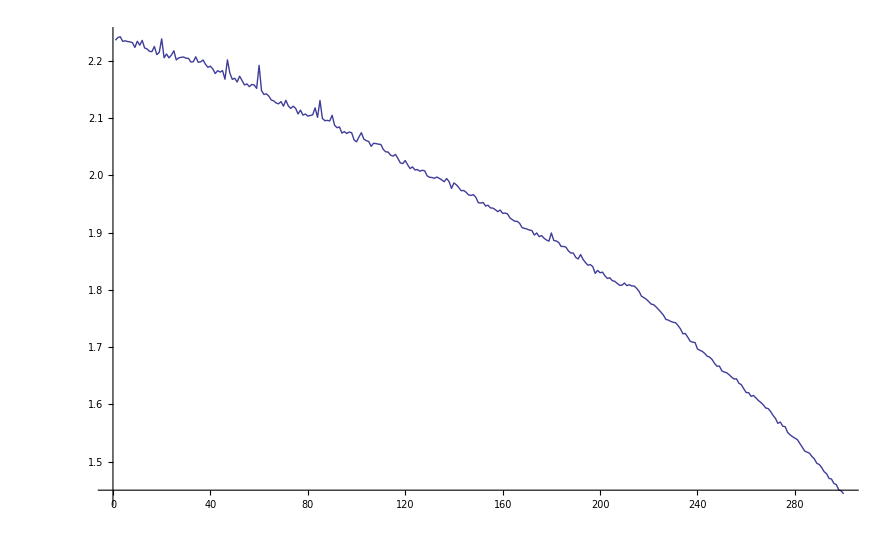

```mathematica
(* Example of RMSE versus # of generations for a large population (~200 reservoirs)
```

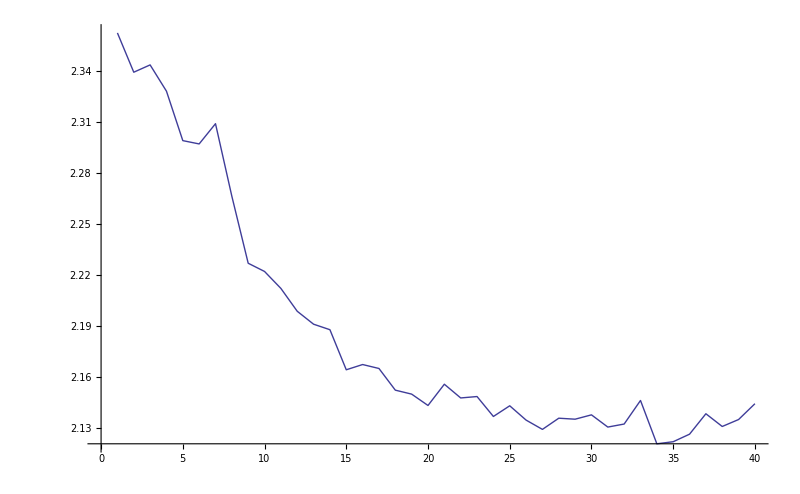
```mathematica
(* Example of RMSE vs # of generations for a small population (~50). Local minima is reached quickly. *)
-Graphics-
```

### Discovering best combinations of input data

```mathematica
inputResults=Table[{Mean[SimulateManyDates[300,SP500,2400,400,4,130,.05,.7,12,0,180][[All,2]]],randomizedInputList},{100}];
Sort[inputResults,#1[[1]]>#2[[1]]&]
```

{2,3,4,5,7,11,13,14,17,18,20,23}

{2,3,4,5,6,7,9,10,15,20,21,23}

{2,3,4,5,6,8,12,13,14,20,21,22}

{2,3,4,5,10,12,15,17,19,20,21,23}

{2,3,4,5,7,8,9,11,13,15,16,17}

{2,3,4,5,6,10,12,14,15,18,20,22}

{2,3,4,5,8,9,12,14,15,16,21,22}

{2,3,4,5,6,7,15,16,17,19,20,22}

{2,3,4,5,8,10,12,14,15,18,20,21}

{2,3,4,5,6,7,8,10,14,15,19,23}

{2,3,4,5,6,10,11,13,17,18,19,22}

{2,3,4,5,6,7,8,9,10,12,20,23}

{2,3,4,5,6,10,14,15,20,21,22,23}

{2,3,4,5,8,9,10,11,12,14,17,21}

{2,3,4,5,6,7,15,17,18,19,21,23}

{2,3,4,5,7,11,13,14,18,20,21,23}

{2,3,4,5,6,7,8,10,15,20,22,23}

{2,3,4,5,6,7,9,11,12,14,15,22}

{2,3,4,5,6,8,12,15,17,18,19,22}

{2,3,4,5,7,8,10,11,13,14,15,17}

{2,3,4,5,6,7,11,12,13,16,19,23}

{2,3,4,5,10,16,18,19,20,21,22,23}

{2,3,4,5,7,8,10,12,14,18,19,20}

{2,3,4,5,9,11,13,14,15,20,21,22}

{2,3,4,5,6,13,14,15,18,19,20,22}

{2,3,4,5,10,11,13,14,15,16,17,20}

{2,3,4,5,6,7,11,13,15,18,20,22}

{2,3,4,5,7,8,9,11,15,16,19,22}

{2,3,4,5,8,9,12,13,17,18,19,21}

{2,3,4,5,6,7,9,10,12,13,16,22}

{2,3,4,5,6,8,10,11,13,16,19,22}

{2,3,4,5,8,11,13,14,16,20,22,23}

{2,3,4,5,9,10,11,12,13,14,15,20}

{2,3,4,5,7,8,10,15,17,18,20,22}

{2,3,4,5,6,9,10,15,17,20,22,23}

{2,3,4,5,6,7,8,9,15,18,19,21}

{2,3,4,5,9,10,12,15,16,17,21,22}

{2,3,4,5,6,8,12,13,16,17,19,20}

{2,3,4,5,6,7,13,14,16,21,22,23}

{2,3,4,5,10,13,14,16,17,18,21,22}

{2,3,4,5,6,10,14,15,16,19,20,23}

{2,3,4,5,6,7,8,12,14,18,19,21}

{2,3,4,5,6,11,12,14,15,17,20,23}

{2,3,4,5,6,11,15,16,17,20,21,22}

{2,3,4,5,7,8,9,10,12,13,16,23}

{2,3,4,5,6,10,11,12,17,20,22,23}

{2,3,4,5,7,8,9,12,13,14,15,20}

{2,3,4,5,8,9,12,15,16,17,21,23}

{2,3,4,5,8,11,12,15,17,18,19,20}

{2,3,4,5,7,8,13,16,19,21,22,23}

{2,3,4,5,10,11,15,16,18,19,21,23}

{2,3,4,5,7,8,11,14,15,19,22,23}

{2,3,4,5,7,8,9,13,15,16,20,23}

{2,3,4,5,7,9,10,12,13,15,16,19}

{2,3,4,5,8,11,14,17,18,19,20,23}

{2,3,4,5,8,10,15,17,18,21,22,23}

{2,3,4,5,9,10,11,12,13,14,18,22}

{2,3,4,5,6,7,9,13,16,18,20,23}

{2,3,4,5,6,8,9,12,14,17,19,20}

{2,3,4,5,8,9,10,12,14,16,17,19}

{2,3,4,5,6,9,10,12,13,15,16,20}

{2,3,4,5,7,13,17,18,19,20,21,22}

{2,3,4,5,7,8,12,15,16,20,21,22}

{2,3,4,5,12,14,15,16,18,19,21,22}

{2,3,4,5,6,7,8,11,12,15,20,22}

{2,3,4,5,7,9,11,15,16,18,22,23}

{2,3,4,5,7,8,10,11,12,16,19,22}

{2,3,4,5,7,9,13,14,17,18,22,23}

{2,3,4,5,10,12,13,14,16,21,22,23}

{2,3,4,5,9,11,12,13,14,17,18,23}

{2,3,4,5,7,10,13,15,17,19,20,22}

{2,3,4,5,8,9,10,11,15,20,21,22}

{2,3,4,5,7,8,10,15,16,20,22,23}

{2,3,4,5,8,11,12,13,14,15,20,21}

{2,3,4,5,7,13,14,15,17,18,20,23}

{2,3,4,5,7,11,13,15,16,18,19,21}

{2,3,4,5,6,7,9,11,14,16,18,23}

{2,3,4,5,7,9,10,11,14,15,20,22}

{2,3,4,5,10,11,12,14,15,17,19,22}

{2,3,4,5,8,9,11,13,14,15,21,22}

{2,3,4,5,6,8,9,12,15,17,19,22}

{2,3,4,5,6,8,13,14,15,16,17,18}

{2,3,4,5,8,10,12,13,15,16,21,22}

{2,3,4,5,6,7,10,13,14,17,19,22}

{2,3,4,5,7,8,10,17,18,19,21,22}

{2,3,4,5,8,9,10,13,15,16,18,22}

{2,3,4,5,6,8,11,12,13,14,19,20}

{2,3,4,5,10,12,13,15,17,20,21,22}

{2,3,4,5,6,8,9,13,15,18,19,22}

{2,3,4,5,6,12,13,16,17,19,20,21}

{2,3,4,5,7,8,10,15,18,19,21,23}

{2,3,4,5,6,14,15,16,17,18,22,23}

{2,3,4,5,7,8,9,10,11,13,18,23}

{2,3,4,5,6,9,11,12,14,17,19,22}

{2,3,4,5,6,11,15,16,17,18,19,21}

{2,3,4,5,6,8,9,14,17,18,19,21}

{2,3,4,5,8,11,12,15,16,17,19,23}

{2,3,4,5,6,8,10,13,16,18,20,21}

{2,3,4,5,11,12,16,18,19,21,22,23}

{2,3,4,5,6,7,10,13,14,16,17,19}

{{0.562,{2,3,4,5,6,7,9,10,15,20,21,23}},{0.56,{2,3,4,5,6,10,14,15,16,19,20,23}},{0.558,{2,3,4,5,6,11,15,16,17,20,21,22}},{0.554,{2,3,4,5,6,7,9,13,16,18,20,23}},{0.554,{2,3,4,5,6,7,8,9,15,18,19,21}},{0.552,{2,3,4,5,6,11,15,16,17,18,19,21}},{0.552,{2,3,4,5,6,10,12,14,15,18,20,22}},{0.55,{2,3,4,5,6,8,10,13,16,18,20,21}},{0.55,{2,3,4,5,7,8,10,17,18,19,21,22}},{0.55,{2,3,4,5,6,7,11,12,13,16,19,23}},{0.548,{2,3,4,5,6,7,9,11,14,16,18,23}},{0.548,{2,3,4,5,6,9,10,15,17,20,22,23}},{0.548,{2,3,4,5,6,13,14,15,18,19,20,22}},{0.548,{2,3,4,5,6,7,15,17,18,19,21,23}},{0.546,{2,3,4,5,6,10,11,13,17,18,19,22}},{0.544,{2,3,4,5,6,9,11,12,14,17,19,22}},{0.544,{2,3,4,5,8,11,14,17,18,19,20,23}},{0.542,{2,3,4,5,6,7,10,13,14,16,17,19}},{0.54,{2,3,4,5,6,8,11,12,13,14,19,20}},{0.54,{2,3,4,5,8,11,12,15,17,18,19,20}},{0.54,{2,3,4,5,7,8,9,11,15,16,19,22}},{0.54,{2,3,4,5,6,7,11,13,15,18,20,22}},{0.538,{2,3,4,5,6,7,8,11,12,15,20,22}},{0.538,{2,3,4,5,6,7,8,10,14,15,19,23}},{0.536,{2,3,4,5,6,8,9,14,17,18,19,21}},{0.536,{2,3,4,5,6,8,9,12,15,17,19,22}},{0.536,{2,3,4,5,6,7,9,10,12,13,16,22}},{0.536,{2,3,4,5,6,7,15,16,17,19,20,22}},{0.534,{2,3,4,5,6,7,8,10,15,20,22,23}},{0.53,{2,3,4,5,6,10,14,15,20,21,22,23}},{0.53,{2,3,4,5,6,7,8,9,10,12,20,23}},{0.528,{2,3,4,5,6,8,9,13,15,18,19,22}},{0.528,{2,3,4,5,6,8,9,12,14,17,19,20}},{0.528,{2,3,4,5,6,8,12,13,16,17,19,20}},{0.528,{2,3,4,5,6,7,9,11,12,14,15,22}},{0.526,{2,3,4,5,7,8,10,15,18,19,21,23}},{0.526,{2,3,4,5,6,12,13,16,17,19,20,21}},{0.526,{2,3,4,5,6,7,10,13,14,17,19,22}},{0.526,{2,3,4,5,6,8,13,14,15,16,17,18}},{0.526,{2,3,4,5,7,13,17,18,19,20,21,22}},{0.526,{2,3,4,5,6,7,13,14,16,21,22,23}},{0.524,{2,3,4,5,6,11,12,14,15,17,20,23}},{0.524,{2,3,4,5,6,8,10,11,13,16,19,22}},{0.522,{2,3,4,5,6,14,15,16,17,18,22,23}},{0.522,{2,3,4,5,6,9,10,12,13,15,16,20}},{0.522,{2,3,4,5,8,10,15,17,18,21,22,23}},{0.522,{2,3,4,5,6,8,12,13,14,20,21,22}},{0.52,{2,3,4,5,7,8,12,15,16,20,21,22}},{0.52,{2,3,4,5,6,10,11,12,17,20,22,23}},{0.52,{2,3,4,5,6,7,8,12,14,18,19,21}},{0.52,{2,3,4,5,7,8,10,15,17,18,20,22}},{0.52,{2,3,4,5,8,9,12,13,17,18,19,21}},{0.518,{2,3,4,5,8,11,12,15,16,17,19,23}},{0.516,{2,3,4,5,10,12,15,17,19,20,21,23}},{0.514,{2,3,4,5,7,11,13,15,16,18,19,21}},{0.514,{2,3,4,5,7,8,10,11,12,16,19,22}},{0.51,{2,3,4,5,7,10,13,15,17,19,20,22}},{0.508,{2,3,4,5,7,8,9,10,11,13,18,23}},{0.508,{2,3,4,5,8,9,10,11,12,14,17,21}},{0.506,{2,3,4,5,7,8,11,14,15,19,22,23}},{0.506,{2,3,4,5,7,11,13,14,17,18,20,23}},{0.504,{2,3,4,5,10,11,12,14,15,17,19,22}},{0.504,{2,3,4,5,9,11,12,13,14,17,18,23}},{0.504,{2,3,4,5,6,8,12,15,17,18,19,22}},{0.502,{2,3,4,5,7,13,14,15,17,18,20,23}},{0.502,{2,3,4,5,7,8,13,16,19,21,22,23}},{0.502,{2,3,4,5,7,8,9,11,13,15,16,17}},{0.5,{2,3,4,5,8,9,12,14,15,16,21,22}},{0.498,{2,3,4,5,7,8,10,11,13,14,15,17}},{0.498,{2,3,4,5,8,10,12,14,15,18,20,21}},{0.496,{2,3,4,5,7,9,13,14,17,18,22,23}},{0.496,{2,3,4,5,7,9,11,15,16,18,22,23}},{0.496,{2,3,4,5,10,11,15,16,18,19,21,23}},{0.496,{2,3,4,5,7,8,10,12,14,18,19,20}},{0.492,{2,3,4,5,8,10,12,13,15,16,21,22}},{0.49,{2,3,4,5,10,13,14,16,17,18,21,22}},{0.49,{2,3,4,5,8,11,13,14,16,20,22,23}},{0.488,{2,3,4,5,7,9,10,12,13,15,16,19}},{0.486,{2,3,4,5,8,9,10,12,14,16,17,19}},{0.484,{2,3,4,5,12,14,15,16,18,19,21,22}},{0.482,{2,3,4,5,8,9,11,13,14,15,21,22}},{0.482,{2,3,4,5,7,8,9,12,13,14,15,20}},{0.482,{2,3,4,5,7,11,13,14,18,20,21,23}},{0.48,{2,3,4,5,8,9,12,15,16,17,21,23}},{0.478,{2,3,4,5,11,12,16,18,19,21,22,23}},{0.478,{2,3,4,5,8,9,10,11,15,20,21,22}},{0.478,{2,3,4,5,9,10,11,12,13,14,18,22}},{0.478,{2,3,4,5,10,16,18,19,20,21,22,23}},{0.476,{2,3,4,5,7,8,9,10,12,13,16,23}},{0.47,{2,3,4,5,7,8,9,13,15,16,20,23}},{0.466,{2,3,4,5,7,8,10,15,16,20,22,23}},{0.464,{2,3,4,5,10,12,13,14,16,21,22,23}},{0.464,{2,3,4,5,9,11,13,14,15,20,21,22}},{0.462,{2,3,4,5,8,9,10,13,15,16,18,22}},{0.46,{2,3,4,5,7,9,10,11,14,15,20,22}},{0.46,{2,3,4,5,9,10,12,15,16,17,21,22}},{0.456,{2,3,4,5,8,11,12,13,14,15,20,21}},{0.456,{2,3,4,5,10,11,13,14,15,16,17,20}},{0.454,{2,3,4,5,10,12,13,15,17,20,21,22}},{0.448,{2,3,4,5,9,10,11,12,13,14,15,20}}}

```mathematica
sortedResult=Sort[inputResults,#1[[1]]>#2[[1]]&]
```

{{0.562,{2,3,4,5,6,7,9,10,15,20,21,23}},{0.56,{2,3,4,5,6,10,14,15,16,19,20,23}},{0.558,{2,3,4,5,6,11,15,16,17,20,21,22}},{0.554,{2,3,4,5,6,7,9,13,16,18,20,23}},{0.554,{2,3,4,5,6,7,8,9,15,18,19,21}},{0.552,{2,3,4,5,6,11,15,16,17,18,19,21}},{0.552,{2,3,4,5,6,10,12,14,15,18,20,22}},{0.55,{2,3,4,5,6,8,10,13,16,18,20,21}},{0.55,{2,3,4,5,7,8,10,17,18,19,21,22}},{0.55,{2,3,4,5,6,7,11,12,13,16,19,23}},{0.548,{2,3,4,5,6,7,9,11,14,16,18,23}},{0.548,{2,3,4,5,6,9,10,15,17,20,22,23}},{0.548,{2,3,4,5,6,13,14,15,18,19,20,22}},{0.548,{2,3,4,5,6,7,15,17,18,19,21,23}},{0.546,{2,3,4,5,6,10,11,13,17,18,19,22}},{0.544,{2,3,4,5,6,9,11,12,14,17,19,22}},{0.544,{2,3,4,5,8,11,14,17,18,19,20,23}},{0.542,{2,3,4,5,6,7,10,13,14,16,17,19}},{0.54,{2,3,4,5,6,8,11,12,13,14,19,20}},{0.54,{2,3,4,5,8,11,12,15,17,18,19,20}},{0.54,{2,3,4,5,7,8,9,11,15,16,19,22}},{0.54,{2,3,4,5,6,7,11,13,15,18,20,22}},{0.538,{2,3,4,5,6,7,8,11,12,15,20,22}},{0.538,{2,3,4,5,6,7,8,10,14,15,19,23}},{0.536,{2,3,4,5,6,8,9,14,17,18,19,21}},{0.536,{2,3,4,5,6,8,9,12,15,17,19,22}},{0.536,{2,3,4,5,6,7,9,10,12,13,16,22}},{0.536,{2,3,4,5,6,7,15,16,17,19,20,22}},{0.534,{2,3,4,5,6,7,8,10,15,20,22,23}},{0.53,{2,3,4,5,6,10,14,15,20,21,22,23}},{0.53,{2,3,4,5,6,7,8,9,10,12,20,23}},{0.528,{2,3,4,5,6,8,9,13,15,18,19,22}},{0.528,{2,3,4,5,6,8,9,12,14,17,19,20}},{0.528,{2,3,4,5,6,8,12,13,16,17,19,20}},{0.528,{2,3,4,5,6,7,9,11,12,14,15,22}},{0.526,{2,3,4,5,7,8,10,15,18,19,21,23}},{0.526,{2,3,4,5,6,12,13,16,17,19,20,21}},{0.526,{2,3,4,5,6,7,10,13,14,17,19,22}},{0.526,{2,3,4,5,6,8,13,14,15,16,17,18}},{0.526,{2,3,4,5,7,13,17,18,19,20,21,22}},{0.526,{2,3,4,5,6,7,13,14,16,21,22,23}},{0.524,{2,3,4,5,6,11,12,14,15,17,20,23}},{0.524,{2,3,4,5,6,8,10,11,13,16,19,22}},{0.522,{2,3,4,5,6,14,15,16,17,18,22,23}},{0.522,{2,3,4,5,6,9,10,12,13,15,16,20}},{0.522,{2,3,4,5,8,10,15,17,18,21,22,23}},{0.522,{2,3,4,5,6,8,12,13,14,20,21,22}},{0.52,{2,3,4,5,7,8,12,15,16,20,21,22}},{0.52,{2,3,4,5,6,10,11,12,17,20,22,23}},{0.52,{2,3,4,5,6,7,8,12,14,18,19,21}},{0.52,{2,3,4,5,7,8,10,15,17,18,20,22}},{0.52,{2,3,4,5,8,9,12,13,17,18,19,21}},{0.518,{2,3,4,5,8,11,12,15,16,17,19,23}},{0.516,{2,3,4,5,10,12,15,17,19,20,21,23}},{0.514,{2,3,4,5,7,11,13,15,16,18,19,21}},{0.514,{2,3,4,5,7,8,10,11,12,16,19,22}},{0.51,{2,3,4,5,7,10,13,15,17,19,20,22}},{0.508,{2,3,4,5,7,8,9,10,11,13,18,23}},{0.508,{2,3,4,5,8,9,10,11,12,14,17,21}},{0.506,{2,3,4,5,7,8,11,14,15,19,22,23}},{0.506,{2,3,4,5,7,11,13,14,17,18,20,23}},{0.504,{2,3,4,5,10,11,12,14,15,17,19,22}},{0.504,{2,3,4,5,9,11,12,13,14,17,18,23}},{0.504,{2,3,4,5,6,8,12,15,17,18,19,22}},{0.502,{2,3,4,5,7,13,14,15,17,18,20,23}},{0.502,{2,3,4,5,7,8,13,16,19,21,22,23}},{0.502,{2,3,4,5,7,8,9,11,13,15,16,17}},{0.5,{2,3,4,5,8,9,12,14,15,16,21,22}},{0.498,{2,3,4,5,7,8,10,11,13,14,15,17}},{0.498,{2,3,4,5,8,10,12,14,15,18,20,21}},{0.496,{2,3,4,5,7,9,13,14,17,18,22,23}},{0.496,{2,3,4,5,7,9,11,15,16,18,22,23}},{0.496,{2,3,4,5,10,11,15,16,18,19,21,23}},{0.496,{2,3,4,5,7,8,10,12,14,18,19,20}},{0.492,{2,3,4,5,8,10,12,13,15,16,21,22}},{0.49,{2,3,4,5,10,13,14,16,17,18,21,22}},{0.49,{2,3,4,5,8,11,13,14,16,20,22,23}},{0.488,{2,3,4,5,7,9,10,12,13,15,16,19}},{0.486,{2,3,4,5,8,9,10,12,14,16,17,19}},{0.484,{2,3,4,5,12,14,15,16,18,19,21,22}},{0.482,{2,3,4,5,8,9,11,13,14,15,21,22}},{0.482,{2,3,4,5,7,8,9,12,13,14,15,20}},{0.482,{2,3,4,5,7,11,13,14,18,20,21,23}},{0.48,{2,3,4,5,8,9,12,15,16,17,21,23}},{0.478,{2,3,4,5,11,12,16,18,19,21,22,23}},{0.478,{2,3,4,5,8,9,10,11,15,20,21,22}},{0.478,{2,3,4,5,9,10,11,12,13,14,18,22}},{0.478,{2,3,4,5,10,16,18,19,20,21,22,23}},{0.476,{2,3,4,5,7,8,9,10,12,13,16,23}},{0.47,{2,3,4,5,7,8,9,13,15,16,20,23}},{0.466,{2,3,4,5,7,8,10,15,16,20,22,23}},{0.464,{2,3,4,5,10,12,13,14,16,21,22,23}},{0.464,{2,3,4,5,9,11,13,14,15,20,21,22}},{0.462,{2,3,4,5,8,9,10,13,15,16,18,22}},{0.46,{2,3,4,5,7,9,10,11,14,15,20,22}},{0.46,{2,3,4,5,9,10,12,15,16,17,21,22}},{0.456,{2,3,4,5,8,11,12,13,14,15,20,21}},{0.456,{2,3,4,5,10,11,13,14,15,16,17,20}},{0.454,{2,3,4,5,10,12,13,15,17,20,21,22}},{0.448,{2,3,4,5,9,10,11,12,13,14,15,20}}}

### Data Analysis

```mathematica
(* RC Simulations with no Genetic Algorithm Optimization *)
(*
SimulateManyDates[numberReservoirs_,input_,startDay_,trainDays_,testDays_,Nodes_,connectivity_,SRadius_,K_,Leakage_,β_,random_]
*)
SimulateManyDates[100,SP500,200,400,4,130,.05,.7,30,0,180,"no"]
```

```mathematica
(* Correctly predicted SP500 direction in 57.5% of days traded over 18 months *)
```

{0.575{2,3,4,5,6,8,12,19,24,28,30,32,37,45,45,47,52,59,61,69,77,79,79,81,85,86,87,88,91,97}}

{{7/25/2011,0.4},{8/1/2011,0.4},{8/8/2011,1.},{8/15/2011,0.6},{8/22/2011,0.6},{8/29/2011,0.4},{9/6/2011,0.8},{9/13/2011,0.4},{9/20/2011,0.6},{9/27/2011,0.4},{10/4/2011,0.6},{10/11/2011,0.4},{10/18/2011,1.},{10/25/2011,1.},{11/1/2011,0.4},{11/8/2011,0.2},{11/15/2011,0.4},{11/22/2011,0.2},{11/30/2011,0.4},{12/7/2011,0.6},{12/14/2011,0.6},{12/21/2011,0.8},{12/29/2011,0.2},{1/6/2012,0.8},{1/13/2012,0.6},{1/23/2012,0.6},{1/30/2012,0.4},{2/6/2012,0.6},{2/13/2012,0.6},{2/21/2012,0.8},{2/28/2012,0.8},{3/6/2012,0.8},{3/13/2012,0.8},{3/20/2012,0.2},{3/27/2012,0.6},{4/3/2012,0.6},{4/11/2012,0.8},{4/18/2012,0.2},{4/25/2012,0.},{5/2/2012,0.2},{5/9/2012,0.8},{5/16/2012,0.8},{5/23/2012,0.4},{5/31/2012,0.8},{6/7/2012,0.4},{6/14/2012,0.2},{6/21/2012,0.6},{6/28/2012,0.4},{7/6/2012,0.8},{7/13/2012,0.6},{7/20/2012,0.8},{7/27/2012,0.6},{8/3/2012,1.},{8/10/2012,0.4},{8/17/2012,0.6},{8/24/2012,0.6},{8/31/2012,0.6},{9/10/2012,1.},{9/17/2012,0.4},{9/24/2012,0.6},{10/1/2012,0.4},{10/8/2012,0.6},{10/15/2012,0.6},{10/22/2012,0.8},{10/31/2012,0.6},{11/7/2012,0.6},{11/14/2012,0.4},{11/21/2012,0.4},{11/29/2012,0.8},{12/6/2012,0.6},{12/13/2012,0.4},{12/20/2012,0.6},{12/28/2012,0.6},{1/7/2013,1.},{1/14/2013,1.},{1/22/2013,0.4},{1/29/2013,0.6},{2/5/2013,0.6},{2/12/2013,0.6},{2/20/2013,0.2}}

```mathematica
list=%
```

{{7/25/2011,0.4},{8/1/2011,0.4},{8/8/2011,1.},{8/15/2011,0.6},{8/22/2011,0.6},{8/29/2011,0.4},{9/6/2011,0.8},{9/13/2011,0.4},{9/20/2011,0.6},{9/27/2011,0.4},{10/4/2011,0.6},{10/11/2011,0.4},{10/18/2011,1.},{10/25/2011,1.},{11/1/2011,0.4},{11/8/2011,0.2},{11/15/2011,0.4},{11/22/2011,0.2},{11/30/2011,0.4},{12/7/2011,0.6},{12/14/2011,0.6},{12/21/2011,0.8},{12/29/2011,0.2},{1/6/2012,0.8},{1/13/2012,0.6},{1/23/2012,0.6},{1/30/2012,0.4},{2/6/2012,0.6},{2/13/2012,0.6},{2/21/2012,0.8},{2/28/2012,0.8},{3/6/2012,0.8},{3/13/2012,0.8},{3/20/2012,0.2},{3/27/2012,0.6},{4/3/2012,0.6},{4/11/2012,0.8},{4/18/2012,0.2},{4/25/2012,0.},{5/2/2012,0.2},{5/9/2012,0.8},{5/16/2012,0.8},{5/23/2012,0.4},{5/31/2012,0.8},{6/7/2012,0.4},{6/14/2012,0.2},{6/21/2012,0.6},{6/28/2012,0.4},{7/6/2012,0.8},{7/13/2012,0.6},{7/20/2012,0.8},{7/27/2012,0.6},{8/3/2012,1.},{8/10/2012,0.4},{8/17/2012,0.6},{8/24/2012,0.6},{8/31/2012,0.6},{9/10/2012,1.},{9/17/2012,0.4},{9/24/2012,0.6},{10/1/2012,0.4},{10/8/2012,0.6},{10/15/2012,0.6},{10/22/2012,0.8},{10/31/2012,0.6},{11/7/2012,0.6},{11/14/2012,0.4},{11/21/2012,0.4},{11/29/2012,0.8},{12/6/2012,0.6},{12/13/2012,0.4},{12/20/2012,0.6},{12/28/2012,0.6},{1/7/2013,1.},{1/14/2013,1.},{1/22/2013,0.4},{1/29/2013,0.6},{2/5/2013,0.6},{2/12/2013,0.6},{2/20/2013,0.2}}

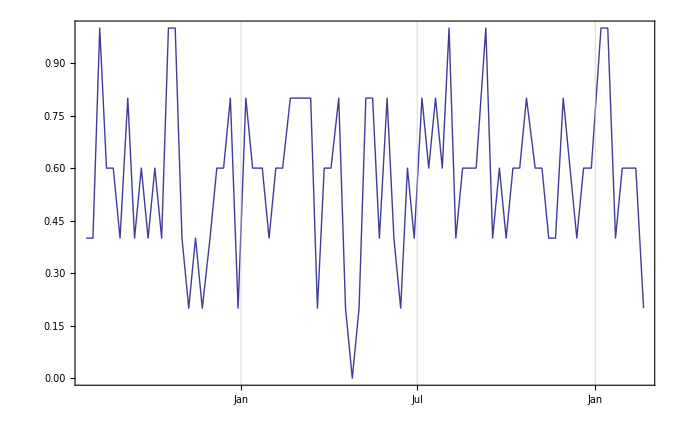

```mathematica
Quiet[DateListPlot[list,Joined->True]]
```

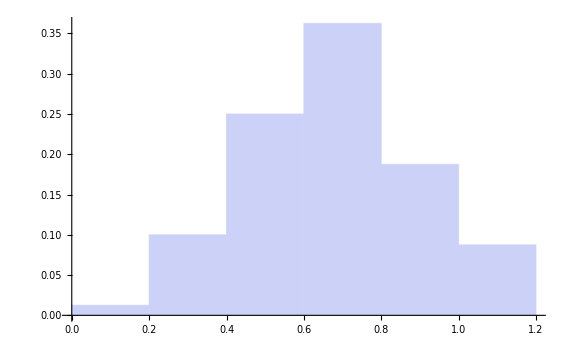

0.575

0.228091

```mathematica
Histogram[list[[All,2]],Automatic,"Probability"]
Mean[list[[All,2]]]
StandardDeviation[list[[All,2]]]
(* Histogram of weekly results *)
```

#### SimulateManyDates[300, SP500, 2400, 400, 4, 130, .05, .7, 14, 0, 180] -> 80 permutations over 500 days. Top 59%

```mathematica
{{0.59,{2,3,4,5,6,8,9,11,13,16,17,18,21,22}},{0.572,{2,3,4,5,6,7,9,10,11,13,15,17,18,21}},{0.5699999999999998,{2,3,4,5,6,8,11,12,13,14,15,16,17,22}},{0.5640000000000001,{2,3,4,5,6,7,13,15,17,18,19,20,21,22}},{0.564,{2,3,4,5,6,7,8,9,10,11,16,18,21,22}},{0.5619999999999997,{2,3,4,5,6,7,9,11,13,14,18,19,20,22}},{0.5619999999999999,{2,3,4,5,6,7,8,9,11,12,14,17,21,22}},{0.5579999999999999,{2,3,4,5,6,8,9,11,12,14,17,19,20,22}},{0.5539999999999999,{2,3,4,5,7,8,9,12,13,16,17,18,20,21}},{0.5539999999999999,{2,3,4,5,6,7,10,11,13,15,16,18,19,22}},{0.552,{2,3,4,5,6,7,8,10,11,14,18,19,20,22}},{0.5519999999999998,{2,3,4,5,6,8,9,11,13,16,18,19,20,22}},{0.5519999999999997,{2,3,4,5,6,7,8,10,11,13,15,16,18,19}},{0.552,{2,3,4,5,6,7,8,9,12,13,14,15,16,21}},{0.5500000000000003,{2,3,4,5,6,7,8,11,12,15,16,18,21,22}},{0.5499999999999997,{2,3,4,5,6,7,9,13,14,15,17,18,19,20}},{0.5499999999999999,{2,3,4,5,7,8,9,12,13,17,18,19,20,21}},{0.5499999999999999,{2,3,4,5,6,7,8,11,13,16,17,19,20,21}},{0.548,{2,3,4,5,6,7,11,12,15,16,19,20,21,22}},{0.5479999999999997,{2,3,4,5,6,8,9,10,12,14,15,18,19,20}},{0.5480000000000002,{2,3,4,5,6,7,9,11,14,15,16,18,19,21}},{0.5439999999999998,{2,3,4,5,6,8,9,10,12,13,17,18,19,20}},{0.544,{2,3,4,5,7,9,11,12,15,17,18,19,21,22}},{0.544,{2,3,4,5,6,7,8,9,10,13,15,16,21,22}},{0.5419999999999997,{2,3,4,5,6,7,10,12,14,15,16,17,19,22}},{0.542,{2,3,4,5,6,7,8,9,10,11,14,15,17,20}},{0.54,{2,3,4,5,8,9,10,11,12,13,17,18,19,21}},{0.5400000000000004,{2,3,4,5,6,7,8,9,11,16,17,18,20,22}},{0.5399999999999998,{2,3,4,5,6,8,9,11,12,13,14,19,20,21}},{0.5399999999999999,{2,3,4,5,6,10,11,12,13,15,18,19,21,22}},{0.5379999999999999,{2,3,4,5,6,7,8,11,14,15,19,20,21,22}},{0.5379999999999999,{2,3,4,5,6,7,9,10,11,13,14,19,20,22}},{0.5380000000000001,{2,3,4,5,6,7,8,12,13,15,16,17,19,21}},{0.538,{2,3,4,5,6,10,12,13,15,16,18,19,20,22}},{0.5359999999999999,{2,3,4,5,8,11,12,13,14,15,16,17,18,19}},{0.5339999999999998,{2,3,4,5,7,8,9,10,13,16,19,20,21,22}},{0.5339999999999998,{2,3,4,5,6,9,11,14,16,17,19,20,21,22}},{0.534,{2,3,4,5,6,7,12,14,15,16,17,19,20,21}},{0.534,{2,3,4,5,6,7,9,12,14,17,18,20,21,22}},{0.5319999999999997,{2,3,4,5,6,7,8,10,14,15,16,17,19,20}},{0.532,{2,3,4,5,6,8,9,10,12,13,15,17,20,21}},{0.5299999999999998,{2,3,4,5,6,7,8,10,12,13,15,16,17,22}},{0.53,{2,3,4,5,6,7,9,11,12,18,19,20,21,22}},{0.5280000000000001,{2,3,4,5,6,7,9,10,11,12,14,15,19,21}},{0.5260000000000001,{2,3,4,5,6,7,10,12,14,17,18,19,21,22}},{0.5260000000000001,{2,3,4,5,7,8,9,10,12,13,15,16,18,21}},{0.5240000000000002,{2,3,4,5,7,8,9,11,14,16,18,19,21,22}},{0.5240000000000001,{2,3,4,5,7,8,9,11,14,15,16,17,18,20}},{0.5219999999999998,{2,3,4,5,6,8,10,11,13,15,16,18,20,22}},{0.522,{2,3,4,5,6,8,9,10,13,15,16,17,20,22}},{0.52,{2,3,4,5,7,9,10,13,14,16,17,18,19,20}},{0.52,{2,3,4,5,6,7,11,12,14,16,19,20,21,22}},{0.5199999999999999,{2,3,4,5,8,10,11,12,13,14,16,17,18,22}},{0.5200000000000002,{2,3,4,5,7,8,9,10,11,13,14,15,17,21}},{0.5179999999999999,{2,3,4,5,6,8,9,10,13,14,16,19,21,22}},{0.518,{2,3,4,5,7,9,12,13,16,17,18,20,21,22}},{0.5179999999999997,{2,3,4,5,8,9,13,14,15,17,18,20,21,22}},{0.5160000000000002,{2,3,4,5,7,9,11,12,13,15,16,18,19,21}},{0.5160000000000001,{2,3,4,5,7,9,10,13,14,15,17,19,20,22}},{0.514,{2,3,4,5,7,8,9,10,14,16,17,20,21,22}},{0.5100000000000001,{2,3,4,5,6,9,13,14,15,16,17,20,21,22}},{0.5100000000000001,{2,3,4,5,8,9,10,15,16,17,19,20,21,22}},{0.51,{2,3,4,5,8,9,10,11,13,14,17,18,20,22}},{0.508,{2,3,4,5,7,9,10,11,12,14,17,18,21,22}},{0.5060000000000001,{2,3,4,5,8,9,10,11,13,15,16,18,20,22}},{0.506,{2,3,4,5,8,9,10,11,12,13,15,18,20,21}},{0.506,{2,3,4,5,7,12,13,14,15,16,17,19,20,21}},{0.5020000000000002,{2,3,4,5,7,9,12,14,15,16,18,20,21,22}},{0.4979999999999999,{2,3,4,5,10,11,12,14,15,16,17,18,19,21}},{0.4980000000000001,{2,3,4,5,7,9,10,11,12,14,15,17,19,22}},{0.4980000000000001,{2,3,4,5,8,9,13,14,15,17,19,20,21,22}},{0.49399999999999994,{2,3,4,5,8,9,10,12,15,16,17,19,20,21}},{0.49,{2,3,4,5,7,8,10,12,14,15,16,20,21,22}},{0.49000000000000005,{2,3,4,5,7,8,9,11,12,13,15,17,21,22}},{0.48600000000000015,{2,3,4,5,9,11,12,13,14,16,18,19,20,21}},{0.4860000000000002,{2,3,4,5,7,10,11,12,13,15,16,18,20,22}},{0.4820000000000001,{2,3,4,5,7,8,10,11,12,13,15,16,20,22}},{0.48200000000000004,{2,3,4,5,7,8,9,10,11,12,13,14,15,21}},{0.47999999999999976,{2,3,4,5,7,10,12,13,15,16,17,18,19,22}},{0.46800000000000025,{2,3,4,5,9,10,11,13,14,15,16,19,20,21}}}
(* Top 10 *)
{{5,10},{4,10},{3,10},{2,10},{6,9},{22,8},{11,8},{7,7},{18,7},{17,7},{13,7},{9,7},{21,6},{8,6},{16,5},{20,4},{19,4},{14,4},{12,4},{15,4},{10,3}}
(* Bottom 10 *)
{{5,10},{4,10},{3,10},{2,10},{15,9},{12,8},{13,8},{16,7},{10,7},{21,7},{20,7},{11,6},{7,6},{22,6},{9,6},{8,6},{19,5},{14,5},{17,4},{18,3}}
```

## Backtesting

### • Backtest Definitions

```mathematica
(*If statement for trailing stop w/ Return & Breake*)
dailyReturn[dayNum_,daySignal_]:=Module[{i=1,dropNum,lowVal,highVal,priceClose={0}},
Clear[PNL];

PNL={0};
While[i<Length[SPYInput[[dayNum]]],
If[DateList[SPYInput[[dayNum,i,1]]][[4]]==9 && DateList[SPYInput[[dayNum,i,1]]][[5]]==35,{entryPrice=SPYInput[[dayNum,i,5]],Print["Entry Price = ",entryPrice],highVal=entryPrice,lowVal=entryPrice,exitPrice=entryPrice,dropNum=i}];
PNL=Append[PNL,daySignal*(SPYInput[[dayNum,i,5]]/entryPrice-1)];
priceClose=Append[priceClose,SPYInput[[dayNum,i,5]]];
highVal=Max[priceClose];
lowVal=Min[priceClose];


(*Trailing Stop Orders *)
(*
If[i>dropNum &&daySignal==1 &&SPYInput[[dayNum,i,5]]<.985*highVal,{exitPrice=SPYInput[[dayNum,i,5]],Break[]}];
If[i>dropNum && daySignal==-1 &&SPYInput[[dayNum,i,5]]>1.015*lowVal,{exitPrice=SPYInput[[dayNum,i,5]],Break[]}];
*)
(*
If[i>dropNum &&daySignal==1 &&SPYInput[[dayNum,i,5]]<.99*entryPrice,{exitPrice=SPYInput[[dayNum,i,5]],Break[]}];
If[i>dropNum && daySignal==-1 &&SPYInput[[dayNum,i,5]]>1.01*entryPrice,{exitPrice=SPYInput[[dayNum,i,5]],Break[]}];
*)(*

If[i>dropNum &&daySignal==1 &&SPYInput[[dayNum,i,5]]>1.02*entryPrice,{exitPrice=SPYInput[[dayNum,i,5]],Break[]}];
If[i>dropNum && daySignal==-1 &&SPYInput[[dayNum,i,5]]<.98*entryPrice,{exitPrice=SPYInput[[dayNum,i,5]],Break[]}];
*)

If[DateList[SPYInput[[dayNum,i,1]]][[4]]==15 && DateList[SPYInput[[dayNum,i,1]]][[5]]==55,{exitPrice=SPYInput[[dayNum,i,4]],Print["Exit Price = ",exitPrice],Break[]}];
If[DateList[SPYInput[[dayNum,i,1]]][[4]]==15 && DateList[SPYInput[[dayNum,i,1]]][[5]]==56,{exitPrice=SPYInput[[dayNum,i,4]],Print["Exit Price = ",exitPrice],Break[]}];
If[DateList[SPYInput[[dayNum,i,1]]][[4]]==15 && DateList[SPYInput[[dayNum,i,1]]][[5]]==57,{exitPrice=SPYInput[[dayNum,i,4]],Print["Exit Price = ",exitPrice],Break[]}];

If[DateList[SPYInput[[dayNum,i,1]]][[4]]==16 && DateList[SPYInput[[dayNum,i,1]]][[5]]==00,{exitPrice=SPYInput[[dayNum,i,4]],Break[]}];
(* In case 15:55 Doesn't exist *)
i++];
(* Will need to return exitPrice as well as entryPrice *)
dayReturn=daySignal*(exitPrice/entryPrice-1);
PNL=Drop[PNL,dropNum];
Return[{dayReturn,PNL}];
]

getReturns[sig_]:=Module[{},
For[i=1,i<Length[SPYInput],i++,
If[DateList[StartTestDate][[1;;3]]==DateList[SPYInput[[i,1,1]]][[1;;3]],dayStart=i;Break[]]
];
dailyResults=Table[Quiet[dailyReturn[i,sig[[i+1-dayStart]]]],{i,dayStart,dayStart+Length[sig]-1}];
dailyPerformance=Table[dailyResults[[i]][[1]],{i,Length[dailyResults]}];
dailyPNL=Table[dailyResults[[i]][[2]],{i,Length[dailyResults]}];

Return[{dailyPerformance,dailyPNL}];
]

PortSim[returns_]:=Module[{i},
portval=100;
For[i=1,i<Length[returns],i++,
portval=portval+portval*returns[[i]]
];
SPComparison=(SPYInput[[dayStart+Length[sigbacktest]]][[1,4]]-SPYInput[[dayStart]][[1,4]])/SPYInput[[dayStart]][[1,4]];
Return[{portval/100 -1,SPComparison}];
]
```

### • Run Backtest

Entry Price = 127.96

Exit Price = 127.802

Entry Price = 127.249

Exit Price = 127.72

Entry Price = 127.08

Exit Price = 128.04

Entry Price = 127.85

Exit Price = 127.73

Entry Price = 127.93

Exit Price = 127.98

Entry Price = 129.39

Exit Price = 129.14

Entry Price = 128.66

Exit Price = 129.29

Entry Price = 129.64

Exit Price = 129.63

Entry Price = 128.44

Exit Price = 128.8

Entry Price = 130.06

Exit Price = 129.32

{-0.0109199,0.00911925}

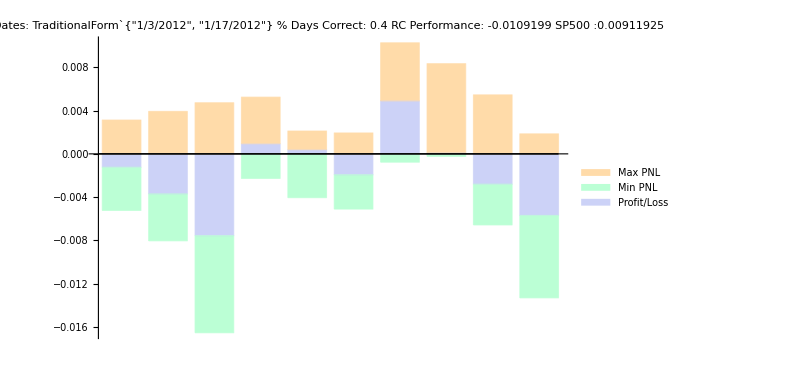

0.4

```mathematica
newbacktest=Quiet[getReturns[sigbacktest]];

portfolioResults=PortSim[newbacktest[[1]]]
bardata=Table[{newbacktest[[1,i]],Min[newbacktest[[2,i]]],Max[newbacktest[[2,i]]]},{i,1,Length[newbacktest[[1]]]}];
BarChart[bardata,ChartLayout->"Stacked",ChartLegends->{"Profit/Loss","Min PNL","Max PNL"},(*PlotLabel->"Dates: " <>ToString[EndTestDate,TraditionalForm] " - "<>ToString[StartTestDate,TraditionalForm]]*)
PlotLabel->("Dates: "<>ToString[{StartTestDate,EndTestDate},TraditionalForm] "\n RC Performance: " <>ToString[portfolioResults[[1]]]"\n SP500 :"  <>ToString[portfolioResults[[2]]] "\n % Days Correct: " <>ToString[N[Count[dailyPerformance,_?Positive]/Length[dailyPerformance]]]),ImageSize->{600,400}]
N[Count[newbacktest[[1]],_?Positive]/Length[newbacktest[[1]]]]
```

```mathematica
sigbacktest
```

sigbacktest

### • Backtest Results

#### 2012 Results - % Difference validateReservoirs[3000., 100., SP500, 2365., 400., 24., .05, 19., .1]; - {Grid Search Bias Only} Nodes = 130, SRad=.7

RC 2012 Performance: 
SP500 2012 Performance:
% Days Correct:

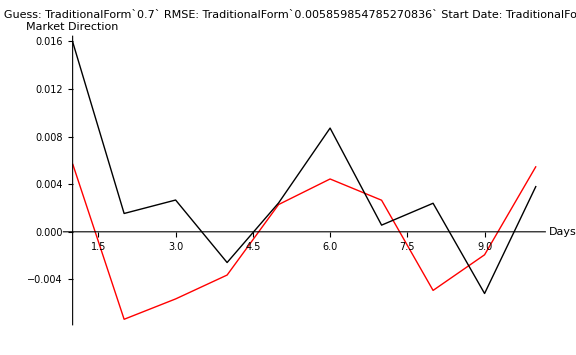
```mathematica
-Graphics-
-Graphics-
```

```mathematica
performance={.7};
sp500={}
original=100;
For[i=1,i<Length[performance]+1,i++,
original=original*(1+performance[[i]]);
Print[original]]
Print[original/100 -1]
N[(52+68+52+52+36+60+52+48+60+60)/10]
```

{0.0537023,0.0357275,-0.0132124,-0.0365492,0.0217097,0.0294831,0.0279246,0.00931008,-0.0311833,0.0148501}

101.624

99.5937

99.5818

99.5118

102.128

99.8818

98.2217

98.768

102.801

101.45

0.0145029

54.

### • Monte-Carlo of Performance

76.7852

42.196

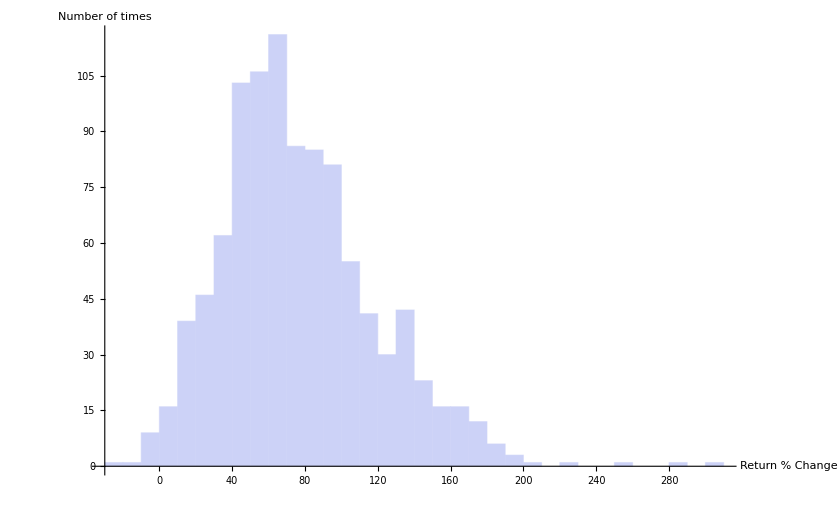

```mathematica
(* Simulation over a year of returns to model returns of Hit Ratio percentage *)
HitRatio=.60;
LargeSimulation=100*ParallelTable[PortfolioSim[HitRatio,SP500,252],{1000}];
Mean[LargeSimulation]
StandardDeviation[LargeSimulation]
Histogram[LargeSimulation,ImageSize->{800,400},AxesLabel->{"Return % Change","Number of times"}]
(* First number is the mean, second is standard deviation *)
```